#### Importing data from Julia

```mathematica
SetDirectory[NotebookDirectory[]];
datawignermix=Import["wignerfunction5_out.dat"];
sp=Import["survivalprobability.dat"];
wg=Import["wignerresults.dat"];
```

```mathematica
wigner2=ListDensityPlot[datawignermix,PlotRange->{{-5,5},{-5,5},{-0.25,0.5}},Frame->True,FrameLabel->{"x","p"},LabelStyle->Directive[Bold,Medium],ColorFunction->"TemperatureMap",PlotLegends->Automatic]
```

-Graphics-

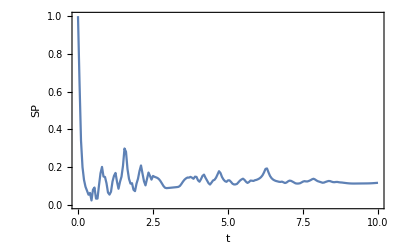

```mathematica
ListPlot[sp,PlotRange->All,Joined->True,Frame->True,FrameLabel->{"t","SP"},LabelStyle->Directive[Bold, Medium]]
```

```mathematica
wn=Table[{wg[[i,1]],wg[[i,3]]},{i,1,Length[wg]}];
```

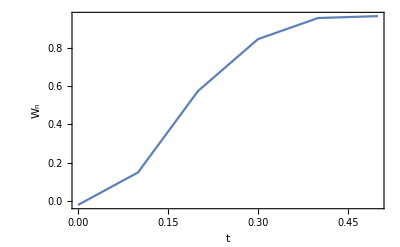

```mathematica
ListPlot[wn,PlotRange->All,Joined->True,Frame->True,FrameLabel->{"t","W_n"},LabelStyle->Directive[Bold, Medium]]
```